# Basic concepts of statistics

Yang Long

#### Modified Variance

σ^2=1/(n-1)(∑_(i=1))^n(x_i-x̄)^2

#### Distribution

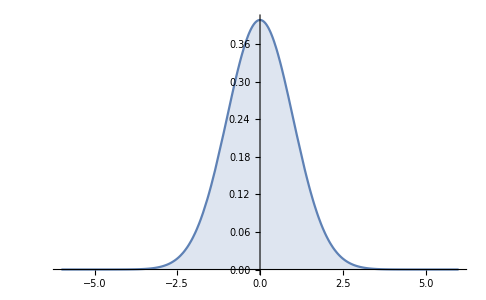

```mathematica
Plot[Evaluate@PDF[NormalDistribution[0,1],x],{x,-6,6},Filling->Axis]
```

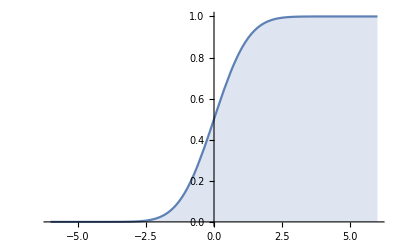

```mathematica
Plot[Evaluate@CDF[NormalDistribution[0,1],x],{x,-6,6},Filling->Axis]
```

#### Pearson Distribution

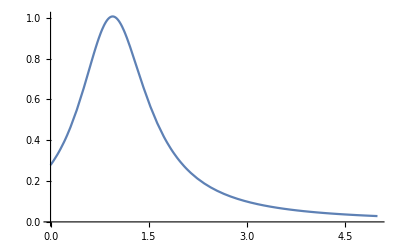

```mathematica
Block[{a=0.05,b0=0.2,b1=0.1,b2=0.5,λ=1.0},Block[{s=NDSolve[{p'[x]/p[x]+(a+(x-λ))/(b0+b1(x-λ)+b2(x-λ)^2)==0,p[λ]==1.0},p,{x,0,5}]},
Plot[p[x]/.s,{x,0,5}]]]
```

#### Poisson Distribution

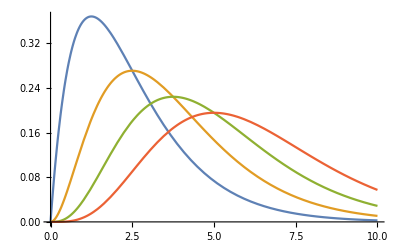

```mathematica
Block[{λ=0.8},Plot[Evaluate@Table[((λ t)^n Exp[-λ t])/(n!),{n,4}],{t,0,10}]]
```

```mathematica
RandomReal[1,5]
```

{0.388524,0.966878,0.426929,0.968823,0.0616149}